# 线性代数

## 超定方程组

```mathematica
m={{1,1},{1,1},{2,4},{2,4}};
b={30,35,90,110};
```

```mathematica
PseudoInverse[m].b//N (*使用伪逆计算超定方程组*)
```

{15.,17.5}

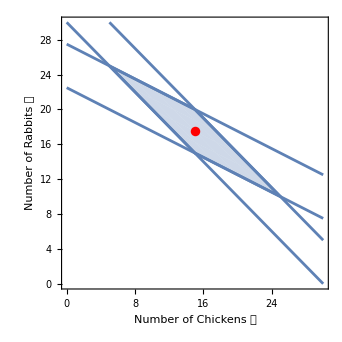

```mathematica
Show[ContourPlot[m.{x1,x2}==b,{x1,0,30},{x2,0,30},PlotTheme->"Detailed",FrameLabel->{"Number of Chickens 🐓","Number of Rabbits 🐇"},Epilog->{Red,PointSize[0.02],Point[{15,17.5}]}](*该点即为平行四边形的中点*),RegionPlot@Parallelogram[LinearSolve[m[[{1,4}]],b[[{1,4}]]],{LinearSolve[m[[{2,4}]],b[[{2,4}]]]-LinearSolve[m[[{1,4}]],b[[{1,4}]]],LinearSolve[m[[{1,3}]],b[[{1,3}]]]-LinearSolve[m[[{1,4}]],b[[{1,4}]]]}](*平行四边形通过一个起点两个向量确定*)]
```

```mathematica
LeastSquares[m,b]//N (*使用最小二乘计算超定方程组*)
```

{15.,17.5}

## 最小二乘法回归

```mathematica
numChickens={32,110,71,79,45,20,56,55,87,68,87,63,31,88};
numRabbits={22,53,39,40,25,15,34,34,52,41,43,33,24,52};
data=Transpose[{numChickens,numRabbits}];
```

```mathematica
(*比例函数*)
```

```mathematica
FindMinimum[Sum[(numRabbits[[i]]-a numChickens[[i]])^2,{i,1,14}],a] (*使用最小二乘定义式*)
```

{245.317,{a→0.551966}}

```mathematica
LeastSquares[Transpose@{numChickens},Transpose@{numRabbits}]//N (*使用最小二乘内置函数*)
```

{{0.551966}}

```mathematica
(*一次函数*)
```

```mathematica
FindMinimum[Sum[(numRabbits[[i]]-(a numChickens[[i]]+c))^2,{i,1,14}],{a,c}] (*使用最小二乘定义式*)
```

{128.669,{a→0.443388,c→7.96413}}

```mathematica
LeastSquares[Transpose@{Table[1,{i,1,14}](*全1列向量*),numChickens},Transpose@{numRabbits}]//N (*使用最小二乘内置函数*)
```

{{7.96413},{0.443388}}

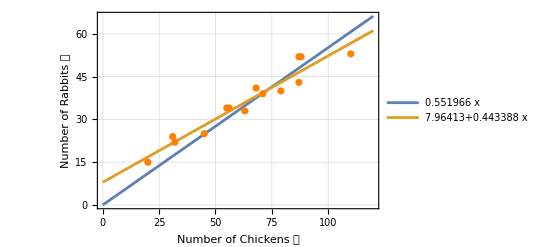

```mathematica
Show[Plot[Evaluate@{Fit[data,{x},x],Fit[data,{1,x},x]}(*使用内置函数拟合*),{x,0,120},PlotTheme->"Detailed",FrameLabel->{"Number of Chickens 🐓","Number of Rabbits 🐇"}],ListPlot[data,PlotStyle->Orange]]
```

a

```mathematica
Correlation[numChickens,numRabbits]StandardDeviation[numRabbits]/StandardDeviation[numChickens](x-Mean[numChickens])+Mean[numRabbits]//N//Simplify (*代入统计公式得到相同的一次函数*)
```

7.96413+0.443388 x